```mathematica
Clear[Dd]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
Dd[n_,0,x_]:=UnitStep[n-1]
Dd[n_,k_,x_]:=Dd[n,k,x]=Sum[Binomial[k,j] Dd[n/(m^(k-j)),j,m+1],{m,x,n^(1/k)},{j,0,k-1}]
yD[n_,k_,x_]:=x^-k Dd[n x^k,k,x+1]
yD1[n_,z_,x_] := Sum[bin[z,k] yD[n,k,x],{k,0,30}]
yDm[n_, k_, x_,m_] := Sum[ (-1)^(k-j)bin[k,j] yD1[n,m j,x],{j,0,k}]
yDm1[n_,z_,x_,m_] := Sum[bin[z,k] yDm[n,k,x,m],{k,0,30}]
yDt[n_, k_, x_,t_] := Sum[ (-1)^(k-j)bin[k,j] t^j yD1[n,j,x],{j,0,k}]
yDt1[n_,z_,x_,t_] := Sum[bin[z,k] yDt[n,k,x,t],{k,0,40}]
```

```mathematica
D[Expand@yD1[100,z,2],z]/.z->0
```

202986703/7096320

```mathematica
Table[yD[100,k,2],{k,0,20}]
```

{1,99,318,1901/4,3379/8,1937/8,1487/16,2983/128,1087/256,229/512,21/1024,1/2048,0,0,0,0,0,0,0,0,0}

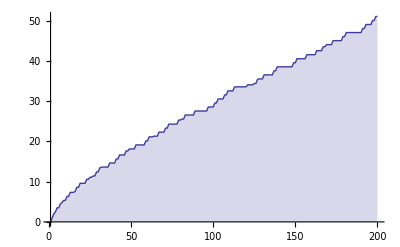

```mathematica
DiscretePlot[D[Expand@yD1[n,z,1],z]/.z->0,{n,1,200}]
```

```mathematica
yDm[100,2,2,2]
```

28763/8

```mathematica
yD[100,2,2]
```

318

```mathematica
D[Expand[yDm1[100,z,1,1]],z]/.z->0
```

428/15

```mathematica
D[Expand[yDm1[100,z,1,2]],z]/.z->0
```

856/15

```mathematica
D[Expand[yDm1[100,z,2,1]],z]/.z->0
```

202986703/7096320

```mathematica
(D[Expand[yDm1[100,z,2,-1]],z]/.z->0)/-1
```

202986703/7096320

```mathematica
(D[Expand[yDt1[10,z,3,.4]],z]/.z->0)-D[yD1[10,z,3],z]/.z->0
```

-0.916291

```mathematica
E^-0.9162911597887128
```

0.4

```mathematica
E^-0.6931471806678493
```

0.5

```mathematica
Clear[D1y1,Dds, yD1]
D1y1[n_,s_,k_,x_]:=D1y1[n,s,k,x]=x Sum[(1+j x)^-s D1y1[n (1+j x)^-1,s,k-1,x],{j,1,(n-1)/x}]
D1y1[n_,s_,0,x_]:=UnitStep[n-1]
Dn[n_, s_, k_, x_] := D1y1[n,s,k,1/x]
Dds[n_,s_,0,x_]:=UnitStep[n-1]
Dds[n_,s_,k_,x_]:=Dds[n,s,k,x]=Sum[Binomial[k,j] m^(-(k-j) s) Dds[Floor[n/(m^(k-j))],s,j,m+1],{m,x,n^(1/k)},{j,0,k-1}]
yDs[n_,s_,k_,x_]:=x^( k(s-1)) Dds[n x^k,s,k,x+1]
yD1o[n_,s_,z_,x_] := yD1[n,s,z,x]=Sum[bin[z,k] yDs[n,s,k,x],{k,0,30}]
yD1[n_,s_,z_,x_] := Sum[bin[z,k] x^( k(s-1)) Dds[n x^k,s,k,x+1],{k,0,Log[n]/(Log[x+1]-Log[x])}]
yDm[n_, s_,k_, x_,m_] := Sum[ (-1)^(k-j)bin[k,j] yD1[n,s,m j,x],{j,0,k}]
yDm1[n_,s_,z_,x_,m_] := Sum[bin[z,k] yDm[n,s,k,x,m],{k,0,Log[If[ 1+1/x<2,1+1/x,2],n]}]
yDm1a[n_,s_,z_,x_,m_] := Table[bin[z,k] yDm[n,s,k,x,m],{k,0,Log[If[ 1+1/x<2,1+1/x,2],n]}]
yDt[n_, s_,k_, x_,t_] := Sum[ (-1)^(k-j)bin[k,j] t^j yD1[n,s,j,x],{j,0,k}]
yDt1[n_,s_,z_,x_,t_] := Sum[bin[z,k] yDt[n,s,k,x,t],{k,0,40}]
l[n_] := Sum[ Log[j]-l[n/j],{j,2,n}]
```

```mathematica
Dn[100,0,2,3]
```

995/3

```mathematica
yD[100,2,3]
```

995/3

```mathematica
D[Expand[yDm1[100,-2,z,1,1]],z]/.z->0
```

1404271/20

```mathematica
(D[Expand[yDm1[100,-2,z,1,2]],z]/.z->0)/2
```

1404271/20

```mathematica
D[Expand[yDm1[100,-2,z,2,1]],z]/.z->0
```

251454465703053807/3307124817920

```mathematica
(D[Expand[yDm1[100,-2,z,2,-3]],z]/.z->0)/-3
```

251454465703053807/3307124817920

```mathematica
N[D[D[yDm1[20,r,z,3,1],z]/.z->0,r]/.r->0]
```

-16.6612

```mathematica
N[D[D[yDm1[20,r,z,3,3],z]/.z->0,r]/.r->0]/3
```

-16.6612

```mathematica
N[D[D[yDt1[20,r,z,1,1],z]/.z->0,r]/.r->0]
```

-19.3301

```mathematica
N[D[D[yDt1[20,r,z,1,.5],z]/.z->0,r]/.r->0]
```

-19.2657

```mathematica
(D[Expand[yDt1[20,3,z,4,.73]],z]/.z->0)-D[yD1[20,3,z,4],z]/.z->0
```

-0.31471

```mathematica
Log[.73]
```

-0.314711

```mathematica
Clear[ds]
ds[n_, a_, k_, x_] := ds[n,a,k,x]=Sum[ ds[n/(i j^a),a,k-1],{i,1+x,n,x},{j,1+x,(n/i)^(1/a),x}]
ds[n_, a_, 0,x_] := UnitStep[n-1]
```

```mathematica
aa[n_, k_] := Sum[ j^k,{j,1,n^(1/k)}]
```

```mathematica
100^(1/(-2))
```

1/10

```mathematica
N@Sum[ 1/(m!) (-1)^(k+1)/k   (Limit[D[ x/Log[1+x],{x,m}],x->0]) (y^(r-1) Zeta[ r,1+y])^(m+k),{k,1,20},{m,0,20}]/.{y->2,r->2}
```

0.789602

```mathematica
N[y^(r-1) Zeta[r,1+y]/.{y->2,r->2}]
```

0.789868

```mathematica
Clear[Dds]
Dds[n_,s_,0,x_]:=UnitStep[n-1]
Dds[n_,s_,k_,x_]:=Dds[n,s,k,x]=Sum[Binomial[k,j] m^(-(k-j) s) Dds[Floor[n/(m^(k-j))],s,j,m+1],{m,x,n^(1/k)},{j,0,k-1}]
yDs[n_,s_,k_,x_]:=x^( k(s-1)) Dds[n x^k,s,k,x+1]
```

```mathematica
N@Sum[ 1/(m!) (-1)^(k+1)/k   (Limit[D[ x/Log[1+x],{x,m}],x->0])  yDs[100,2,m+k+1,3],{k,1,13},{m,0,13}]
```

0.672226

```mathematica
N@yDs[100,2,2,3]
```

0.672226

```mathematica
Table[Chop[ 1/((r+I)-1)-N[y^((r+I)-1) Zeta[(r+I),1+y]/.y->100000]],{r,1,5}]
```

{4.99999×10^-6,4.99998×10^-6,4.99997×10^-6,4.99997×10^-6,4.99996×10^-6}